# Bin Size and Goodness of Fit

```mathematica
n= 200;
μ=10;
σ=1;
Data=RandomVariate[NormalDistribution[μ,σ],n];
```

{9.92828,1.00908}

{0.0717198,0.00908328}

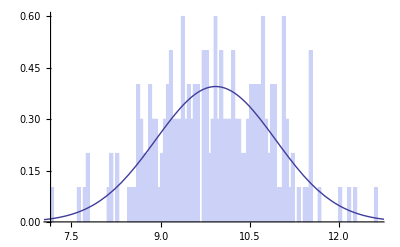

0.11474

```mathematica
binSize=0.05;
j=HistogramList[Data,{binSize},"PDF"];
Hdata=Table[{(j[[1,i]]+j[[1,i+1]])/2,j[[2,i]]},{i,1,Length[j[[1]]]-1}];
{α,β}={a,b}/.FindFit[Hdata,(ⅇ^(-(-a+x)^2/(2 b^2)))/(b √(2 π)),{a,b},x]
Δ={Abs[α-μ],Abs[β-σ]}
Show[
Histogram[Data,{binSize},"PDF"],
Plot[(ⅇ^(-(-α+x)^2/(2 β^2)))/(β √(2 π)),{x,μ-3σ,μ+3σ}]
]
χsq=√(Sum[((ⅇ^(-(-α+Hdata[[i,1]])^2/(2 β^2)))/(β √(2 π))-Hdata[[i,2]])^2,{i,1,Length[Hdata]}]/Length[Hdata])
```

```mathematica
Error=Table[
j=HistogramList[Data,{binSize},"PDF"];
Hdata=Table[{(j[[1,i]]+j[[1,i+1]])/2,j[[2,i]]},{i,1,Length[j[[1]]]-1}];
{α,β}={a,b}/.FindFit[Hdata,(ⅇ^(-(-a+x)^2/(2 b^2)))/(b √(2 π)),{a,b},x];
Δ={binSize,Abs[α-μ],Abs[β-σ],√(Sum[((ⅇ^(-(-α+Hdata[[i,1]])^2/(2 β^2)))/(β √(2 π))-Hdata[[i,2]])^2,{i,1,Length[Hdata]}]/Length[Hdata])},{binSize,0.1,4,0.1}];
```

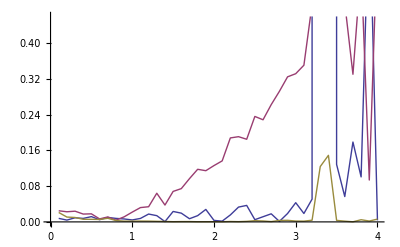

```mathematica
ListPlot[
{Table[Error[[i,1;;2]],{i,1,Length[Error]}],
Table[Error[[i,1;;3;;2]],{i,1,Length[Error]}],
Table[Error[[i,1;;4;;3]],{i,1,Length[Error]}]
}
,Joined->True]
```

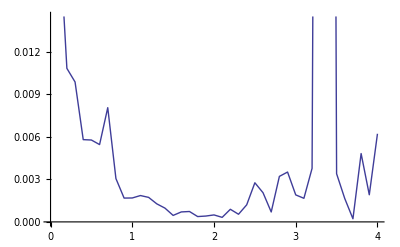

```mathematica
ListPlot[
Table[Error[[i,1;;4;;3]],{i,1,Length[Error]}]
,Joined->True]
```